## Мухамадиев Владимир

# Задание 4

## Загрузка и предварительная обработка

```mathematica
data1=Import[NotebookDirectory[]<>"\\bio-celegans.txt","Data"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,1,Length[data1]}];
```

```mathematica
g1=Graph[el1];
```

```mathematica
data2=Import[NotebookDirectory[]<>"\\bio-diseasome.txt","Data"];
```

```mathematica
el2=Table[data2⟦i,1⟧<->data2⟦i,2⟧,{i,1,Length[data2]}];
```

```mathematica
g2=Graph[el2];
```

```mathematica
data3=Import[NotebookDirectory[]<>"\\cit-HepTh.txt","Data"];
```

```mathematica
el3=Table[data3⟦i,1⟧<->data3⟦i,2⟧,{i,1,Length[data3]}];
```

```mathematica
g3=Graph[el3];
```

```mathematica
MinMaxNormalization[data_]:=Table[(data⟦i⟧-Min[data])/(Max[data]-Min[data]),{i,1,Length[data]}]
```

## 1. Complementary cumulative distribution function (Survival function)

```mathematica
CCDF[arr_,nbins_]:=Table[N[{i,SurvivalFunction[EmpiricalDistribution[arr],i]}],{i,Min[arr],Max[arr],(Max[arr]-Min[arr])/(nbins-1)}]
```

### Экспоненциальное распределение

PDF(x)=λ ⅇ^(-λ x)
CDF(x)=1-ⅇ^(-λ x)
CCDF(x)=ⅇ^(-λ x)
ln(CCDF(x))=-λ x
При отображении x→ln(CCDF(x)), получаем линейную зависимость вида f(x)=-a x, где a=λ

#### λ=2

```mathematica
edλ2=RandomVariate[ExponentialDistribution[2],100000];
```

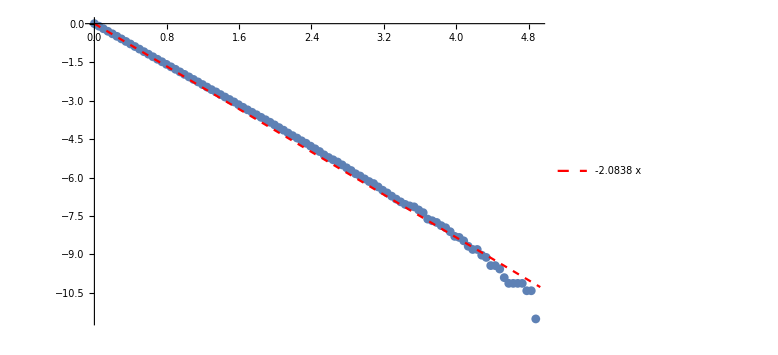

```mathematica
Module[{in=CCDF[edλ2,100],out={}},out={in⟦All,1⟧,Log[in⟦All,2⟧]}ᵀ⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x,IncludeConstantBasis->False]]],{x,in⟦1,1⟧,in⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

#### λ=4

```mathematica
edλ4=RandomVariate[ExponentialDistribution[4],100000];
```

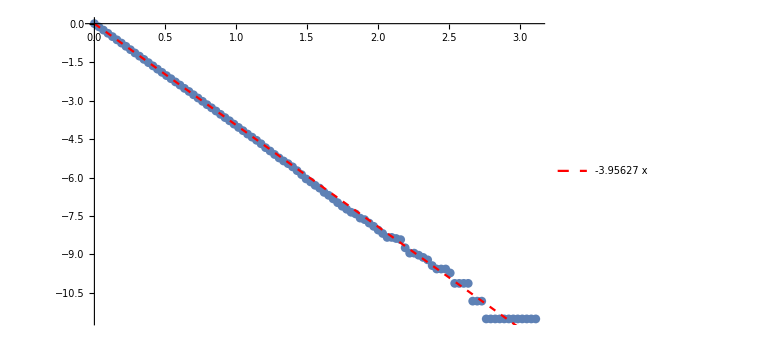

```mathematica
Module[{in=CCDF[edλ4,100],out={}},out={in⟦All,1⟧,Log[in⟦All,2⟧]}ᵀ⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x,IncludeConstantBasis->False]]],{x,in⟦1,1⟧,in⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

### Степенное распределение

PDF(x)=(k(x_min))^k/x^(k+1)
CDF(x)=1-(x_min/x)^k
CCDF(x)=(x_min/x)^k
ln(CCDF(x))=k ln (x_min)-k ln(x)
При отображении ln(x)→ln(CCDF(x)), получаем линейную зависимость вида f(x)=-a x+b, где a=k

#### x_min=4,k=3

```mathematica
pdxm4k3=RandomVariate[ParetoDistribution[4,3],100000];
```

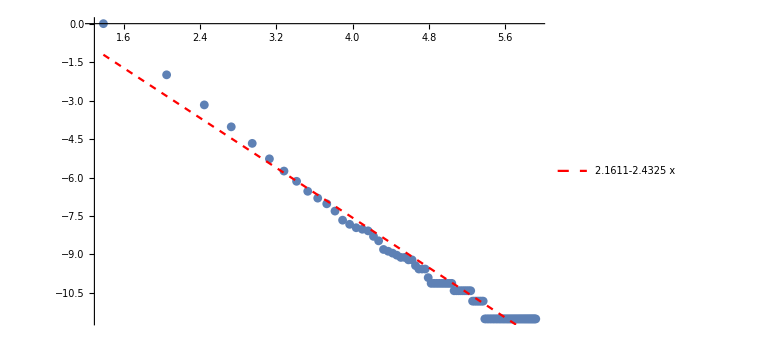

```mathematica
Module[{in=CCDF[pdxm4k3,100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

#### x_min=1,k=2

```mathematica
pdxm1k2=RandomVariate[ParetoDistribution[1,2],100000];
```

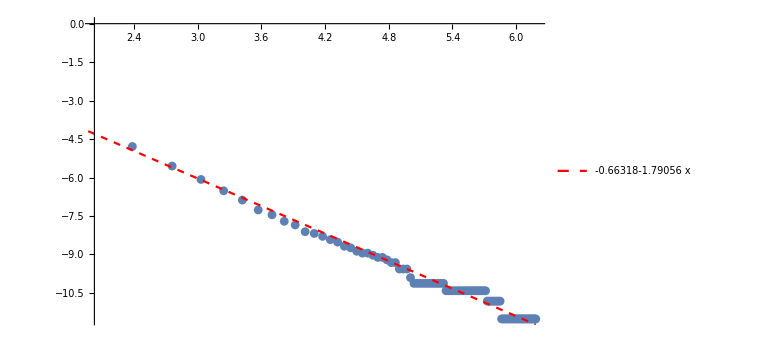

```mathematica
Module[{in=CCDF[pdxm1k2,100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

### Распределение степеней вершин в заданных сетях

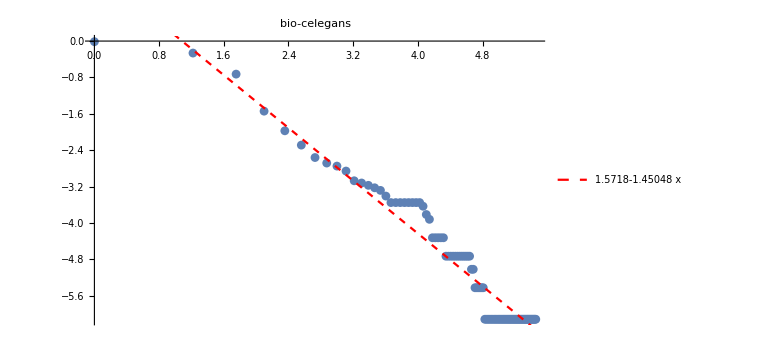

```mathematica
Module[{in=CCDF[VertexDegree[g1],100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],PlotLabel->"bio-celegans",ImageSize->Large]]
```

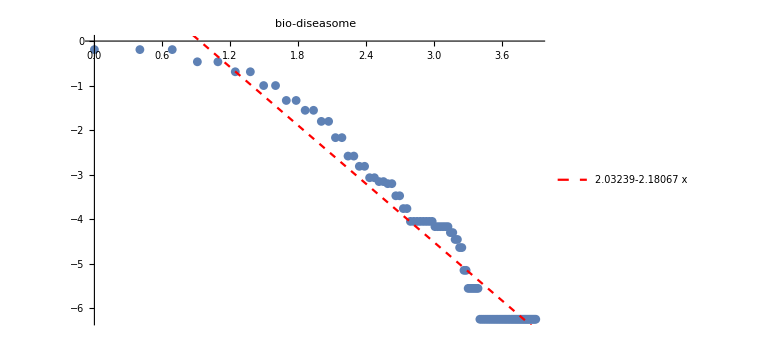

```mathematica
Module[{in=CCDF[VertexDegree[g2],100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],PlotLabel->"bio-diseasome",ImageSize->Large]]
```

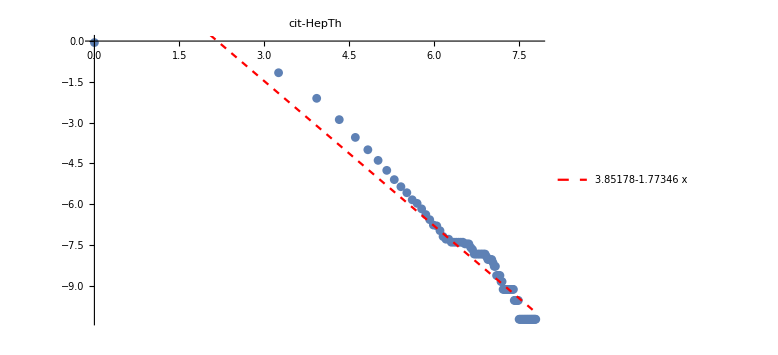

```mathematica
Module[{in=CCDF[VertexDegree[g3],100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],PlotLabel->"cit-HepTh",ImageSize->Large]]
```

### Распределение степеней вершин в модели Барабаши-Альберт

PDF(k)=2 m^2 k^-3
CDF(k)=1-m^2 k^-2
CCDF(k)=m^2 k^-2
ln(CCDF(k))=2 ln (m)-2 ln(k)
При отображении ln(k)→ln(CCDF(k)), получаем линейную зависимость вида f(x)=-2x+a

#### m=2

```mathematica
bam2=RandomGraph[BarabasiAlbertGraphDistribution[10000,2]];
```

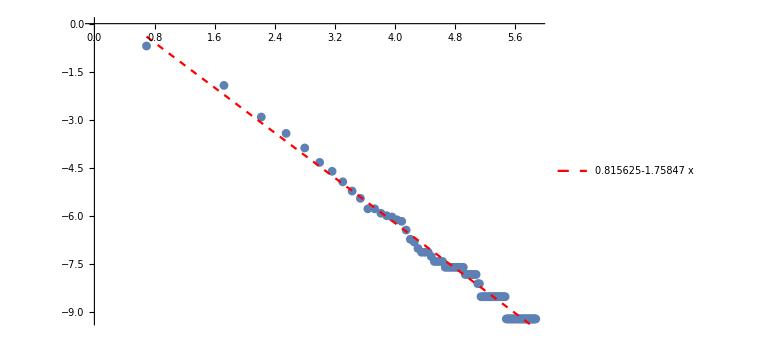

```mathematica
Module[{in=CCDF[VertexDegree[bam2],100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

#### m=4

```mathematica
bam4=RandomGraph[BarabasiAlbertGraphDistribution[10000,4]];
```

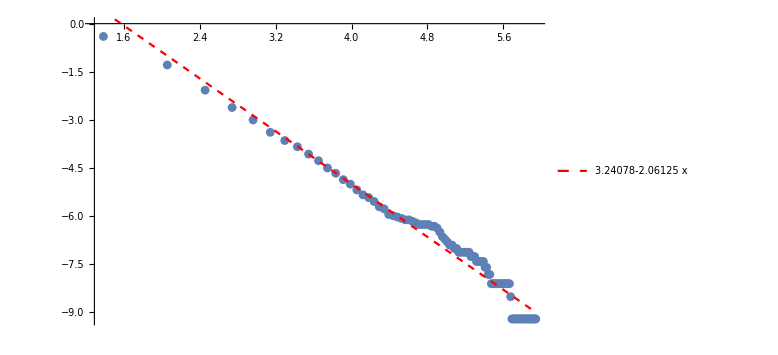

```mathematica
Module[{in=CCDF[VertexDegree[bam4],100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

## 2. Предпочтительное присоединение

### Генерация графа по предпочтительному присоединению с заданными параметрами в виде списка ребер

```mathematica
BarabasiAlbertGraphEdgeList[n_,m_,α_]:=If[ n≤m,EdgeList[CompleteGraph[n]],
(*m==1*)If[m==1,Module[{el=PadRight[{1<->2},n-1,{{}}],pl={},vl=Table[i,{i,1,n}],vla={}},
(*m==1 and α==0*)If[α==0,Do[vla=RandomChoice[vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i,{i,3,n}];el,
(*m==1 and α==1*)If[α==1,pl=Table[1,{i,1,n}];Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i;pl⟦vla⟧=pl⟦vla⟧+1,{i,3,n}];el,
(*m>1 and α≠0 and α≠1*)pl=Table[1,{i,1,n}];Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i;pl⟦vla⟧=(pl⟦vla⟧^(1/α)+1)^α,{i,3,n}];el]]],
(*m>1*)Module[{el=PadRight[EdgeList[CompleteGraph[m]],m n-1/2 m(m+1),{{}}],k=(m(m-1))/2,pl={},vl=Table[i,{i,1,n}],vla={}},
(*m>1 and α==0*)If[α==0,Do[vla=RandomSample[vl⟦1;;i-1⟧,m];Do[k++;el⟦k⟧=vla⟦j⟧<->i,{j,1,m}],{i,m+1,n}];el,
(*m>1 and α==1*)If[α==1,pl=PadRight[Table[m-1,{i,1,m}],n,m];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[k++;el⟦k⟧=vla⟦j⟧<->i;pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+1,{j,1,m}],{i,m+1,n}];el,
(*m>1 and α≠0 and α≠1*)pl=PadRight[Table[(m-1)^α,{i,1,m}],n,m^α];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[k++;el⟦k⟧=vla⟦j⟧<->i;pl⟦vla⟦j⟧⟧=(pl⟦vla⟦j⟧⟧^(1/α)+1)^α,{j,1,m}],{i,m+1,n}];el]]]]]
```

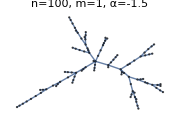
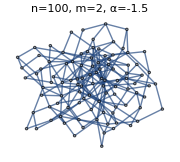
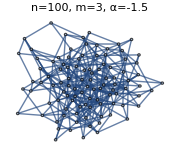
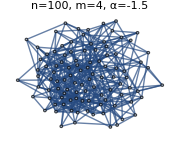
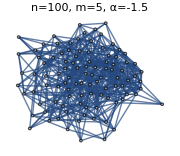
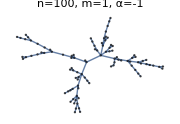
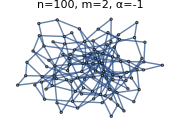
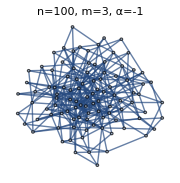
Граф построенный по модели предпочтительного присоединения с заданными параметрами |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Table[Graph[BarabasiAlbertGraphEdgeList[100,p1,p2],PlotLabel->"n=100, m="<>ToString[p1]<>", α="<>ToString[If[p2∈Integers,p2,N[p2]]],ImageSize->Small],{p2,-3/2,5/2,1/2},{p1,1,5,1}],{Style["Граф построенный по модели предпочтительного присоединения с заданными параметрами",16],SpanFromLeft}],Dividers->All,Spacings->{1,1}]
```

### Генерация эволюции роста степени первых m вершин в модели предпочтительного присоединения с заданными параметрами

```mathematica
BarabasiAlbertGraphVertexDegreeEvolution[n_,m_,α_]:=If[ n≤m,PadRight[Table[VertexDegree[CompleteGraph[i]],{i,1,n}]]ᵀ,
(*m==1*)If[m==1,Module[{vd=PadRight[{0,1},n,{{}}],pl={},vl=Table[i,{i,1,n}],vla={}},
(*m==1 and α==0*)If[α==0,Do[vla=RandomChoice[vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧],{i,3,n}];vd,
(*m==1 and α==1*)If[α==1,pl=Table[1,{i,1,n}];Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧];pl⟦vla⟧=pl⟦vla⟧+1,{i,3,n}];vd,
(*m>1 and α≠0 and α≠1*)pl=Table[1,{i,1,n}];Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧];pl⟦vla⟧=(pl⟦vla⟧^(1/α)+1)^α,{i,3,n}];vd]]],
(*m>1*)Module[{vd=PadRight[PadRight[Table[VertexDegree[CompleteGraph[i]],{i,1,m}]],n,{ConstantArray[{},m]}]ᵀ,pl={},vl=Table[i,{i,1,n}],vla={}},
(*m>1 and α==0*)If[α==0,pl=PadRight[Table[m-1,{i,1,m}],n,m];Do[vla=Sort[RandomSample[vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+1;vd⟦j,i⟧=pl⟦j⟧,{j,1,m}],{i,m+1,n}];vd,
(*m>1 and α==1*)If[α==1,pl=PadRight[Table[m-1,{i,1,m}],n,m];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+1;vd⟦j,i⟧=pl⟦j⟧,{j,1,m}],{i,m+1,n}];vd,
(*m>1 and α≠0 and α≠1*)pl=PadRight[Table[(m-1)^α,{i,1,m}],n,m^α];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=(pl⟦vla⟦j⟧⟧^(1/α)+1)^α;vd⟦j,i⟧=pl⟦j⟧^(1/α),{j,1,m}],{i,m+1,n}];vd]]]]]
```

```mathematica
simdata=Import[NotebookDirectory[]<>"\\sim1.m"];(*BarabasiAlbertGraphVertexDegreeEvolution[100000,4,α],α∈{-3,3,0.5}*)
```

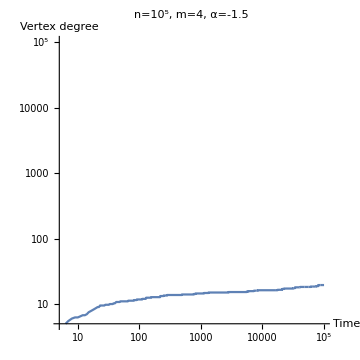
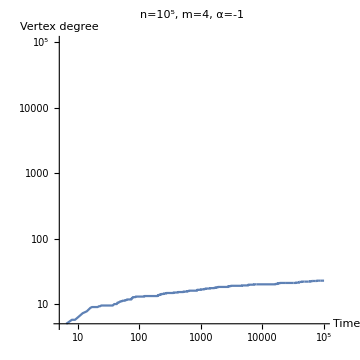
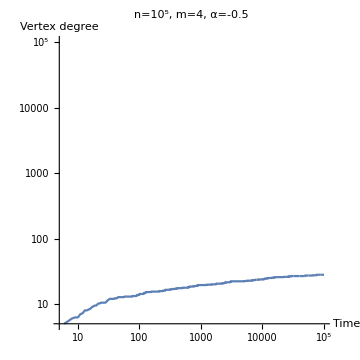
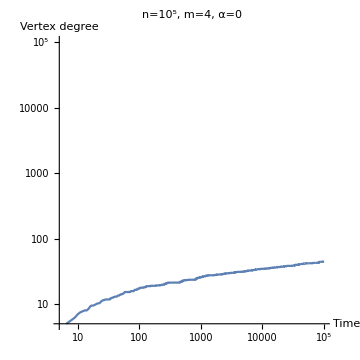
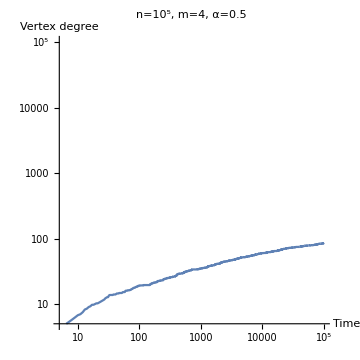
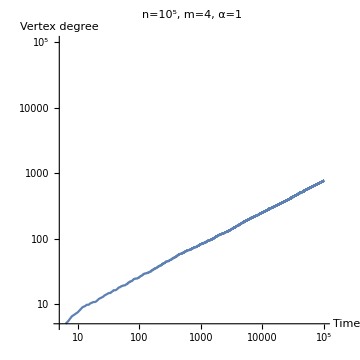
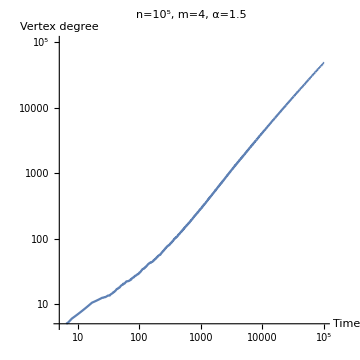
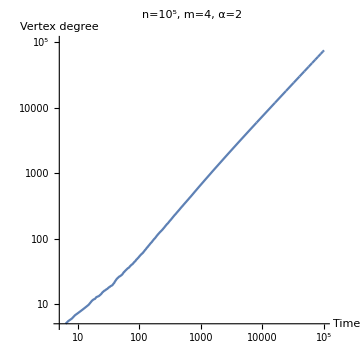
График роста средней степени первых четырех вершин в модели предпочтительного присоединения при различном параметре α |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Partition[Table[ListLogLogPlot[{Range[10^5],Mean[simdata⟦i⟧]}ᵀ,Joined->True,PlotLabel->"n=10^5, m=4, α="<>{"-1.5","-1","-0.5","0","0.5","1","1.5","2","2.5"}⟦i-4⟧,AxesLabel->{"Time","Vertex degree"},ImageSize->Medium,PlotRange->{{5,10^5},{5,10^5}},AspectRatio->1],{i,5,13}],3],{Style["График роста средней степени первых четырех вершин в модели предпочтительного присоединения при различном параметре α",16],SpanFromLeft}],Dividers->All,Spacings->{1,1}]
```

## 3. Модель Бьянкони-Барабаши

```mathematica
BianconiBarabasiGraphEdgeList[m_,α_,μ_]:=Module[{n=Length[μ]},If[ n≤m,EdgeList[CompleteGraph[n]],
(*m==1*)If[m==1,Module[{el=PadRight[{1<->2},n-1,{{}}],pl={},vl=Table[i,{i,1,n}],vla={}},
(*m==1 and α==0*)If[α==0,Do[vla=RandomChoice[μ⟦1;;i-1⟧->vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i,{i,3,n}];el,
(*m==1 and α==1*)If[α==1,pl=μ;Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i;pl⟦vla⟧=pl⟦vla⟧+μ⟦vla⟧,{i,3,n}];el,
(*m>1 and α≠0 and α≠1*)pl=μ;Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];el⟦i-1⟧=vla<->i;pl⟦vla⟧=μ⟦vla⟧((pl⟦vla⟧/μ⟦vla⟧)^(1/α)+1)^α,{i,3,n}];el]]],
(*m>1*)Module[{el=PadRight[EdgeList[CompleteGraph[m]],m n-1/2 m(m+1),{{}}],k=(m(m-1))/2,pl={},vl=Table[i,{i,1,n}],vla={}},
(*m>1 and α==0*)If[α==0,Do[vla=RandomSample[μ⟦1;;i-1⟧->vl⟦1;;i-1⟧,m];Do[k++;el⟦k⟧=vla⟦j⟧<->i,{j,1,m}],{i,m+1,n}];el,
(*m>1 and α==1*)If[α==1,pl=Table[If[i≤m,μ⟦i⟧(m-1),μ⟦i⟧m],{i,1,n}];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[k++;el⟦k⟧=vla⟦j⟧<->i;pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+μ⟦vla⟦j⟧⟧,{j,1,m}],{i,m+1,n}];el,
(*m>1 and α≠0 and α≠1*)pl=Table[If[i≤m,μ⟦i⟧(m-1)^α,μ⟦i⟧m^α],{i,1,n}];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[k++;el⟦k⟧=vla⟦j⟧<->i;pl⟦vla⟦j⟧⟧=μ⟦vla⟦j⟧⟧((pl⟦vla⟦j⟧⟧/μ⟦vla⟦j⟧⟧)^(1/α)+1)^α,{j,1,m}],{i,m+1,n}];el]]]]]]
```

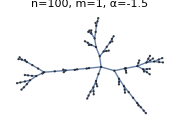
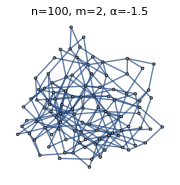
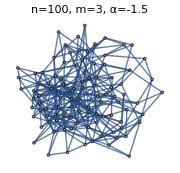
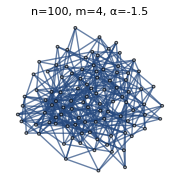
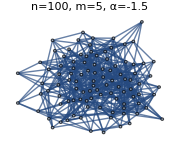
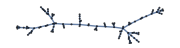
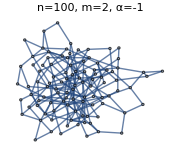
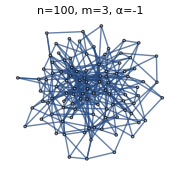
Граф построенный по модели Бьянкони-Барабаши с заданными параметрами |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[Table[Graph[BianconiBarabasiGraphEdgeList[p1,p2,RandomReal[{},100]],PlotLabel->"n=100, m="<>ToString[p1]<>", α="<>ToString[If[p2∈Integers,p2,N[p2]]],ImageSize->Small],{p2,-3/2,5/2,1/2},{p1,1,5,1}],{Style["Граф построенный по модели Бьянкони-Барабаши с заданными параметрами",16],SpanFromLeft}],Dividers->All,Spacings->{1,1}]
```

### Генерация эволюции роста степени первых m вершин в модели Бьянкони-Барабаши с заданными параметрами

```mathematica
BianconiBarabasiGraphVertexDegreeEvolution[m_,α_,μ_]:=Module[{n=Length[μ]},If[ n≤m,PadRight[Table[VertexDegree[CompleteGraph[i]],{i,1,n}]]ᵀ,
(*m==1*)If[m==1,Module[{vd=PadRight[{0,1},n,{{}}],pl={},vl=Table[i,{i,1,n}],vla={}},
(*m==1 and α==0*)If[α==0,Do[vla=RandomChoice[μ⟦1;;i-1⟧->vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧],{i,3,n}];vd,
(*m==1 and α==1*)If[α==1,pl=μ;Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧];pl⟦vla⟧=pl⟦vla⟧+μ⟦vla⟧,{i,3,n}];vd,
(*m>1 and α≠0 and α≠1*)pl=μ;Do[vla=RandomChoice[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧];If[vla==1,vd⟦i⟧=vd⟦i-1⟧+1,vd⟦i⟧=vd⟦i-1⟧];pl⟦vla⟧=μ⟦vla⟧((pl⟦vla⟧/μ⟦vla⟧)^(1/α)+1)^α,{i,3,n}];vd]]],
(*m>1*)Module[{vd=PadRight[PadRight[Table[VertexDegree[CompleteGraph[i]],{i,1,m}]],n,{ConstantArray[{},m]}]ᵀ,pl={},vl=Table[i,{i,1,n}],vla={}},
(*m>1 and α==0*)If[α==0,pl=PadRight[Table[m-1,{i,1,m}],n,m];Do[vla=Sort[RandomSample[μ⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+1;vd⟦j,i⟧=pl⟦j⟧,{j,1,m}],{i,m+1,n}];vd,
(*m>1 and α==1*)If[α==1,pl=Table[If[i≤m,μ⟦i⟧(m-1),μ⟦i⟧m],{i,1,n}];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=pl⟦vla⟦j⟧⟧+μ⟦vla⟦j⟧⟧;vd⟦j,i⟧=pl⟦j⟧/μ⟦j⟧,{j,1,m}],{i,m+1,n}];vd,
(*m>1 and α≠0 and α≠1*)pl=Table[If[i≤m,μ⟦i⟧(m-1)^α,μ⟦i⟧m^α],{i,1,n}];Do[vla=Sort[RandomSample[pl⟦1;;i-1⟧->vl⟦1;;i-1⟧,m]];Do[pl⟦vla⟦j⟧⟧=μ⟦vla⟦j⟧⟧((pl⟦vla⟦j⟧⟧/μ⟦vla⟦j⟧⟧)^(1/α)+1)^α;vd⟦j,i⟧=(pl⟦j⟧/μ⟦j⟧)^(1/α),{j,1,m}],{i,m+1,n}];vd]]]]]]
```

#### Покажем что рост степени вершины в модели Бьянкони-Барабаши подчиняется закону k(t)=(m(t/t_i))^(μ_i/C), где при равномерном распределении C≈1.255

```mathematica
bbvde=Import[NotebookDirectory[]<>"\\sim2.m"];(*bbvde=RandomVariate[UniformDistribution[],100000];bbvde⟦1⟧=0.1;bbvde⟦2⟧=0.2;bbvde⟦3⟧=0.5;bbvde⟦4⟧=0.9;bbvde=BianconiBarabasiGraphVertexDegreeEvolution[4,1,bbvde];*)
```

```mathematica
Show[LogLogPlot[{4 x^(0.1/1.255),4(x/2)^(0.2/1.255),4(x/3)^(0.5/1.255),4(x/4)^(0.9/1.255)},{x,5,100000},PlotLegends->{"4x^(μ_1/1.255)","4(x/2)^(μ_2/1.255)","4(x/3)^(μ_3/1.255)","4(x/4)^(μ_4/1.255)"}],ListLogLogPlot[{{Range[10^5],bbvde⟦1⟧}ᵀ,{Range[10^5],bbvde⟦2⟧}ᵀ,{Range[10^5],bbvde⟦3⟧}ᵀ,{Range[10^5],bbvde⟦4⟧}ᵀ},PlotLegends->{"μ_1=0.1","μ_2=0.2","μ_3=0.5","μ_4=0.9"}],AxesLabel->{"Time","Vertex degree"},PlotLabel->"n=10^5,m=4",ImageSize->Large]
```

-Graphics-

### Посмотрим коэффициент степенного распределения

```mathematica
bbud=VertexDegree[Graph[BianconiBarabasiGraphEdgeList[4,1,RandomVariate[UniformDistribution[],10000]]]];
```

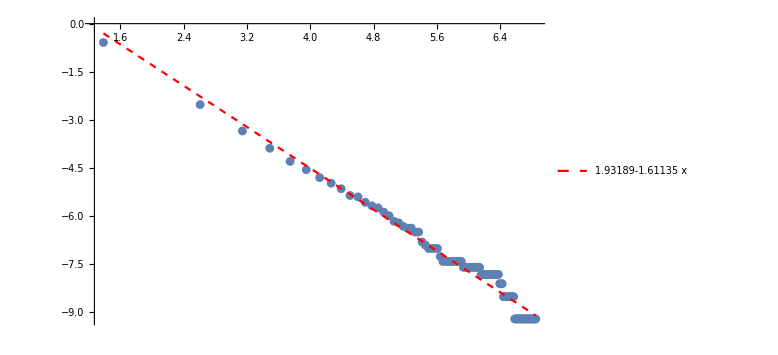

```mathematica
Module[{in=CCDF[bbud,100],out={}},out=Log[in]⟦1;;Length[in]-1⟧;Show[ListPlot[out],Plot[Evaluate[Normal[LinearModelFit[out,x,x]]],{x,out⟦1,1⟧,out⟦-1,1⟧},PlotStyle->{Red,Dashed},PlotLegends->"AllExpressions"],ImageSize->Large]]
```

### Степенные распределения при различных распределениях μ

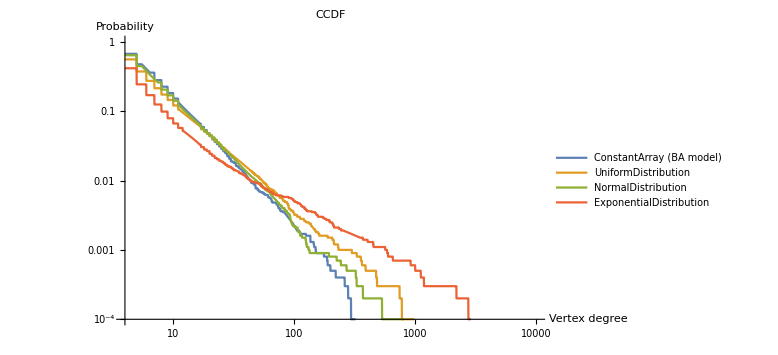

```mathematica
Module[{data={ConstantArray[1,10000],RandomVariate[UniformDistribution[],10000],MinMaxNormalization[RandomVariate[NormalDistribution[],10000]],MinMaxNormalization[RandomVariate[ExponentialDistribution[1],10000]]}},LogLogPlot[Evaluate[Table[SurvivalFunction[EmpiricalDistribution[VertexDegree[Graph[BianconiBarabasiGraphEdgeList[4,1,data⟦i⟧]]]],x],{i,1,Length[data]}]],{x,4,10000},Exclusions->None,PlotLegends->{"ConstantArray (BA model)","UniformDistribution","NormalDistribution","ExponentialDistribution"},AxesLabel->{"Vertex degree","Probability"},PlotLabel->"CCDF",ImageSize->Large]]
```